```mathematica
s4=({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}});
```

```mathematica
x:=1/2 A a1(E^(I(ψa+ϕa))+E^(-I(ψa+ϕa)))+1/2 B(b1 E^(I(ψb+ϕb))+b1c E^(-I(ψb+ϕb)))
y:=1/2 A(a3 E^(I(ψa+ϕa))+a3c E^(-I(ψa+ϕa)))+1/2 B b3(E^(I(ψb+ϕb))+E^(-I(ψb+ϕb)))
```

```mathematica
a1=wx Cos[γ];
a3=wy Sin[γ] Exp[I ph];
a3c=wy Sin[γ] Exp[-I ph];
b1=-Sin[γ]wx Exp[-I ph];
b1c=-Sin[γ]wx Exp[I ph];
b3=wy Cos[γ];
Simplify[-1/2 ⅈ B (a1 b1-a3c b3)]

(*Linear resonance (hamiltonian part: x y)*)
```

1/4 ⅈ B ⅇ^(-ⅈ ph) (wx^2+wy^2) Sin[2 γ]

```mathematica
Hx:=y; Hy:=x; G:={0,Hy,0,-Hx};
```

```mathematica
eqA=Simplify[-I E^(-I(ψa+ϕa)){a1,a2c,a3c,a4c}.s4.G];
eqB=Simplify[-I E^(-I(ψb+ϕb)){b1c,b2c,b3,b4c}.s4.G];
```

```mathematica
Simplify[eqA ⅇ^(1I (ϕa+ψa)) ⅇ^(-1I (ϕb+ψb))]
```

1/2 ⅈ ⅇ^(-ⅈ (2 ph+ϕa+2 ϕb+ψa+2 ψb)) (-A ⅇ^(ⅈ (2 ph+ϕb+ψb)) (1+ⅇ^(2 ⅈ (ϕa+ψa))) wx^2 Cos[γ]^2+B ⅇ^(ⅈ (ph+ϕa+ψa)) (ⅇ^(2 ⅈ ph) wx^2+wy^2+ⅇ^(2 ⅈ (ϕb+ψb)) (wx^2+wy^2)) Cos[γ] Sin[γ]+A ⅇ^(ⅈ (ϕb+ψb)) (1+ⅇ^(2 ⅈ (ph+ϕa+ψa))) wy^2 Sin[γ]^2)

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(1I (ϕa+ψa)) ⅇ^(-1I (ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

1/4 ⅈ B ⅇ^(-ⅈ ph) (wx^2+wy^2) Sin[2 γ]

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(0 I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/4 ⅈ A (wx^2-wy^2+(wx^2+wy^2) Cos[2 γ])

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(0ⅈ (ϕb+ψb)) ⅇ^(-0ⅈ (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

1/4 ⅈ B (-wx^2+wy^2+(wx^2+wy^2) Cos[2 γ])

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(1 I(ϕb+ψb)) ⅇ^(-1 I (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

1/4 ⅈ A ⅇ^(ⅈ ph) (wx^2+wy^2) Sin[2 γ]

```mathematica
(*nonlinear resonance (hamiltonian part: x^4 + 2 x^2 y^2 + y^4+xy)*)
```

```mathematica
Hx:=h1 x(x^2+y^2)+h y; Hy:=y h1(x^2+y^2)+ h x; G:={0,Hy,0,-Hx};
```

```mathematica
eqA=Simplify[-I E^(-I(ψa+ϕa)){a1,a2c,a3c,a4c}.s4.G];
eqB=Simplify[-I E^(-I(ψb+ϕb)){b1c,b2c,b3,b4c}.s4.G];
```

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(2I (ϕa+ψa)) ⅇ^(-2I (ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

1/4 ⅈ A B^2 (a3c b1-a1 b3) (a1 b1+a3c b3) h1

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(1 I (ϕa+ψa))ⅇ^(-1 I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/8 ⅈ B (4 (a1 b1-a3c b3) h+2 A^2 (a1^2 (a3-2 a3c) b1-a3 a3c^2 b1+a1^3 b3+a1 (2 a3-a3c) a3c b3) h1+B^2 (-3 a3c b1^2 b1c+a1 b1 (b1+2 b1c) b3-a3c (2 b1+b1c) b3^2+3 a1 b3^3) h1)

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(-0 I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/4 ⅈ A (A^2 a1^3 (a3-a3c) h1+a1 (A^2 a3 (a3-a3c) a3c+B^2 (a3 b1 b1c-3 a3c b1 b1c+3 a3 b3^2-a3c b3^2)) h1+a1^2 (2 h+B^2 (b1+b1c) b3 h1)-a3 a3c (2 h+B^2 (b1+b1c) b3 h1))

```mathematica
FullSimplify[-1/4 ⅈ A (A^2 a1^3 (a3-a3c) h1+a1 (A^2 a3 (a3-a3c) a3c+B^2 (a3 b1 b1c-3 a3c b1 b1c+3 a3 b3^2-a3c b3^2)) h1+a1^2 (2 h+B^2 (b1+b1c) b3 h1)-a3 a3c (2 h+B^2 (b1+b1c) b3 h1))]
```

-1/32 ⅈ A ⅇ^(-ⅈ ph) (8 ⅇ^(ⅈ ph) h (wx-wy) (wx+wy)+8 ⅇ^(ⅈ ph) h (wx^2+wy^2) Cos[2 γ]+2 h1 wx wy (A^2 (-1+ⅇ^(2 ⅈ ph)) (wx^2+wy^2)-4 B^2 (wx^2-ⅇ^(2 ⅈ ph) wy^2)) Sin[2 γ]+(A^2-2 B^2) (-1+ⅇ^(2 ⅈ ph)) h1 wx (wx-wy) wy (wx+wy) Sin[4 γ])

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(0ⅈ (ϕb+ψb)) ⅇ^(-0ⅈ (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/4 ⅈ B (B^2 b3 (b1 b1c (2 b1+b1c)+(b1+2 b1c) b3^2)+A^2 (a1^2 (3 b1+b1c) b3+a3 a3c (b1+3 b1c) b3+a1 (a3+a3c) (b1 b1c+b3^2)))

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(2I(ϕb+ψb)) ⅇ^(-2 I (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/4 ⅈ A^2 B (2 a1^2 b1c b3+2 a3^2 b1c b3+a1 a3 (b1c^2+b3^2))

```mathematica
Fa=(Fx Exp[I(χx+n s/(2 R))]-(δ+η)/c Fy Exp[I(χy-n s/(2 R))])Exp[I s((νx+νy)/(2 R)+η/2)]
Fb=(Fx Exp[I(χx+n s/(2 R))]-(δ-η)/c Fy Exp[I(χy-n s/(2 R))])Exp[I s((νx+νy)/(2 R)-η/2)]
```

ⅇ^(ⅈ s (η/2+(νx+νy)/(2 R))) (ⅇ^(ⅈ ((n s)/(2 R)+χx)) Fx-(ⅇ^(ⅈ (-(n s)/(2 R)+χy)) Fy (δ+η))/c)

ⅇ^(ⅈ s (-η/2+(νx+νy)/(2 R))) (ⅇ^(ⅈ ((n s)/(2 R)+χx)) Fx-(ⅇ^(ⅈ (-(n s)/(2 R)+χy)) Fy (δ-η))/c)

```mathematica
(*Sextupole(hamiltonian part: x^2y...)*)
```

```mathematica
Hx:=2 x y; Hy:=x^2 - y^2; G:={0,Hy,0,-Hx};
```

```mathematica
eqA=Simplify[-I E^(-I(ψa+ϕa)){a1,a2c,a3c,a4c}.s4.G];
eqB=Simplify[-I E^(-I(ψb+ϕb)){b1c,b2c,b3,b4c}.s4.G];
```

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(1I (ϕa+ψa)) ⅇ^(2I (ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

1/4 ⅈ B^2 (2 a3c b1c b3+a1 (-b1c^2+b3^2))

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(1 I (ϕa+ψa))ⅇ^(-2I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

1/4 ⅈ B^2 (2 a3c b1 b3+a1 (-b1^2+b3^2))

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqA ⅇ^(0 I (ϕa+ψa))ⅇ^(1 I(ϕb+ψb)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/2 ⅈ A B (a1^2 b1c-a3 a3c b1c-a1 (a3+a3c) b3)

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(3ⅈ (ϕb+ψb)) ⅇ^(-0ⅈ (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/4 ⅈ B^2 b1c (b1c^2-3 b3^2)

```mathematica
Simplify[1/(4 π^2)Integrate[Integrate[eqB ⅇ^(2I(ϕb+ψb)) ⅇ^(-2 I (ϕa+ψa)),{ψa,0,2 π}],{ψb,0,2 π}]]
```

-1/4 ⅈ A^2 B (2 a1^2 b1c b3+2 a3^2 b1c b3+a1 a3 (b1c^2+b3^2))

```mathematica
DSolve[{(A[t])'==-(A[t])^2 h1 Sin[ϕa[t]],(ϕa[t])'==-A[t] h1 Cos[ϕa[t]]+n+1/3-δ+Δ},{A[t],ϕa[t]},t]
```

DSolve::derarg: The derivative operator Derivative[1] in A[t]' should act on the pure function.

```mathematica
NDSolve[{A'[t]==-h1 A[t]^2 Sin[ϕa[t]],ϕa'[t]==1/3+n-δ+Δ-h1 A[t] Cos[ϕa[t]],A[0]==1,ϕa[0]==0}/.{n->2,δ->.01,Δ->0,h1->1},{A[t],ϕa[t]},{t,0,4π}]
```

{{A[t]→InterpolatingFunction[…][t],ϕa[t]→InterpolatingFunction[…][t]}}

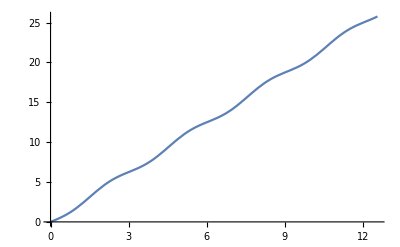

```mathematica
Plot[ϕa[t]/.{ϕa[t]->InterpolatingFunction[…][t]},{t,0,4π}]
```